#### Finding The Quadratic Interpolation Function ϕq:

```mathematica
Solution=FullSimplify[Solve[ϕlo == A + B αlo + c αlo^2 && ϕhi == A + B αhi + c αhi^2 && ϕloPrime == B + 2 c αlo,{A,B,c}]];
AA = FullSimplify[A/.Solution[[1]][[1]]];
BB = FullSimplify[B/.Solution[[1]][[2]]];
CC=  FullSimplify[ c/.Solution[[1]][[3]]];
ϕq[α_]:=AA+BB α + CC α^2;
FullSimplify[ϕq[αlo]]
FullSimplify[ϕq[αhi]]
FullSimplify[D[ϕq[α],α] /.α -> αlo]
AA
BB
CC
```

ϕlo

ϕhi

ϕloPrime

(αhi^2 ϕlo+αlo (αlo ϕhi-2 αhi ϕlo+αhi (-αhi+αlo) ϕloPrime))/(αhi-αlo)^2

(αhi^2 ϕloPrime-αlo (2 ϕhi-2 ϕlo+αlo ϕloPrime))/(αhi-αlo)^2

(ϕhi-ϕlo+(-αhi+αlo) ϕloPrime)/(αhi-αlo)^2

#### Find Minimum Point of Interpolation

```mathematica
minimum = Solve[D[ϕq[α],α]==0,α];
αmin = FullSimplify[α/.minimum[[1]][[1]]]
```

(αhi^2 ϕloPrime-αlo (2 ϕhi-2 ϕlo+αlo ϕloPrime))/(2 (-ϕhi+ϕlo+(αhi-αlo) ϕloPrime))

#### Testing it

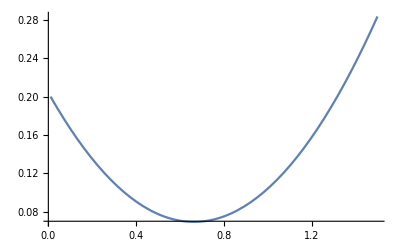

0.663403

```mathematica
Plot[ϕq[α]/.{αlo->0.01,αhi->0.98,ϕlo->0.2,ϕhi->0.1,ϕloPrime->-0.4},{α,0.01,1.5}]
αmin/.{αlo->0.01,αhi->0.98,ϕlo->0.2,ϕhi->0.1,ϕloPrime->-0.4}
```

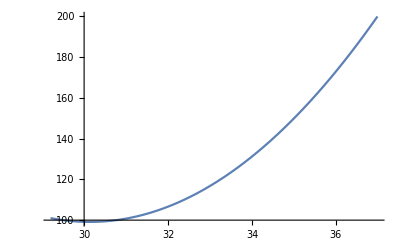

30.1325

```mathematica
Plot[ϕq[α]/.{αlo->29.2,αhi->36.99,ϕlo->101,ϕhi->200,ϕloPrime->-4},{α,29.2,36.99}]
αmin/.{αlo->29.2,αhi->36.99,ϕlo->101,ϕhi->200,ϕloPrime->-4}
```